```mathematica
Clear[d]
FullSimplify[Cos[a-b]*Sin[c]*Sin[d]+Cos[c]*Cos[d]-1/2*(Cos[c-d]*(Cos[a-b]+1)+Cos[c+d]*(1-Cos[a-b]))]
```

0

```mathematica
FullSimplify[Cos[c]*Sin[d]*Cos[b]-Sin[c]*Cos[d]*Cos[a]-(Sin[c+d]*Sin[(a+b)/2]*Sin[(a-b)/2]-Sin[c-d]*(Cos[(a+b)/2]*Cos[(a-b)/2]))]
```

0

```mathematica
Solve[Cos[x-y]==-Cos[x+y]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-π/2},{x→π/2},{y→-π/2},{y→π/2}}

```mathematica
Clear[d];
d=0.5;
FindMinimum[1/2*(Cos[δ]*(Cos[α]+1)+Cos[γ]*(1-Cos[α]))-d*(Sin[γ]*Sin[β/2]*Sin[α/2]-Sin[δ]Cos[β/2]*Cos[α/2]),{α,β,γ,δ}]
FindMinimum[1/2*(Cos[δ]*(Cos[α]+1)+Cos[γ]*(1-Cos[α]))-d*(Sin[γ]*Sin[β/2]*Sin[α/2]-Sin[δ]Cos[β/2]*Cos[α/2]),{{α,0.0},{β,0},{γ,0},{δ,π}}]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{-1.11803,{α→1.87164,β→1.87164,γ→2.67795,δ→3.60524}}

{-1.11803,{α→0.,β→0.,γ→0.,δ→3.60524}}

```mathematica
Clear[d];
Solve[D[1/2*(Cos[δ]*(Cos[α]+1)+Cos[γ]*(1-Cos[α]))-d*(Sin[γ]*Sin[β/2]*Sin[α/2]-Sin[δ]*Cos[β/2]*Cos[α/2]),{{α,β,γ,δ}}]=={0,0,0,0},{α,β,γ,δ}]
```

$Aborted

FindMinimum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

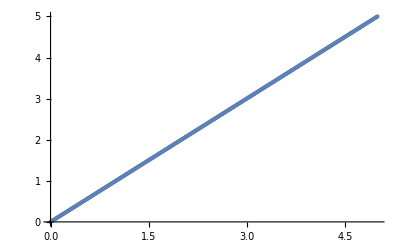

```mathematica
d=0.5;
testlist=Table[{d,Tan[(FindMinimum[1/2*(Cos[δ]*(Cos[α]+1)+Cos[γ]*(1-Cos[α]))-d*(Sin[γ]*Sin[β/2]*Sin[α/2]-Sin[δ]Cos[β/2]*Cos[α/2]),{{α,0.0},{β,0},{γ,0},{δ,π}}][[2,4]]/.Rule->List)[[2]]]},{d,0,5,0.01}];
ListPlot[testlist]
```

```mathematica
DSolve
```